```mathematica
Integrate[PDF[BetaDistribution[a,b],x],{x,α,1},Assumptions->{α>0,α<1,b>0,a>0}]
```

(Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b])/(Gamma[a] Gamma[b])

```mathematica
Ctb[a_,b_,α_]:=((Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b])/(Beta[a,b] Gamma[a+b]))^(-1)
```

```mathematica
Integrate[PDF[BetaDistribution[a,b],x]*Ctb[a,b,α],{x,α,1},Assumptions->{α>0,α<1,a>0,b>0}]
```

1

```mathematica
Integrate[(x^k)*PDF[BetaDistribution[a,b],x]*Ctb[a,b,α],{x,α,1},Assumptions->{α>0,α<1,k>1,k<∞,a>0,b>0}]
```

(Gamma[a+b] (Gamma[b] Gamma[a+k]-Beta[α,a+k,b] Gamma[a+b+k]))/((Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b]) Gamma[a+b+k])

```mathematica
Mtb[a_,b_,α_,k_]:=(Gamma[a+b] (Gamma[b] Gamma[a+k]-Beta[α,a+k,b] Gamma[a+b+k]))/((Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b]) Gamma[a+b+k])
```

```mathematica
Nmom=(0.7*Mtb[1,1,.05,{1,2,3,4,5}]+0.3*Mtb[1/2,1,.05,{1,2,3,4,5}])//N
```

{0.494861,0.322821,0.239408,0.190302,0.157934}

```mathematica
Integrate[(1-x)^k*PDF[BetaDistribution[a,b],x]*Ctb[a,b,α],{x,α,1},Assumptions->{α>0,α<1,k>1,k<∞,a>0,b>0}]
```

(Gamma[a+b] (Gamma[a] Gamma[b+k]-Beta[α,a,b+k] Gamma[a+b+k]))/((Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b]) Gamma[a+b+k])

```mathematica
p0Mtb[a_,b_,α_,k_]:=(Gamma[a+b] (Gamma[a] Gamma[b+k]-Beta[α,a,b+k] Gamma[a+b+k]))/((Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b]) Gamma[a+b+k])
```

```mathematica
.7*p0Mtb[1,1,.05,5]+.3*p0Mtb[1/2,1,.05,5]//N
```

0.153396

```mathematica
Css[S_,r_]:=Binomial[S,r]*(-1)^r
```

```mathematica
1+Sum[Css[5,r]*(0.7*Mtb[1,1,.05,r]+0.3*Mtb[1/2,1,.05,r]),{r,1,5}]//N
```

0.153396

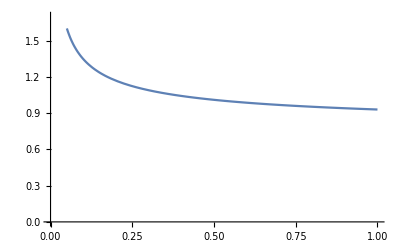

```mathematica
Plot[.7*PDF[BetaDistribution[1,1],x]*Ctb[1,1,.05]+.3*PDF[BetaDistribution[1/2,1],x]*Ctb[1/2,1,.05],{x,.05,1},PlotRange->{{0,1},{0,1.7}}]
```

```mathematica
(0.6*Mtb[2,3,.05,{1,2,3,4,5}]+0.4*Mtb[1/2,1,.05,{1,2,3,4,5}])//N
```

{0.412945,0.224679,0.143144,0.100711,0.0758143}

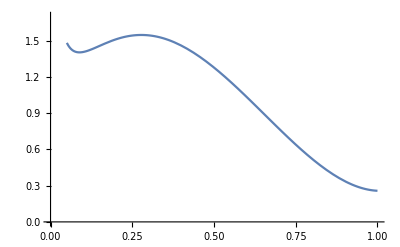

```mathematica
Plot[.6*PDF[BetaDistribution[2,3],x]*Ctb[2,3,.05]+.4*PDF[BetaDistribution[1/2,1],x]*Ctb[1/2,1,.05],{x,.05,1},PlotRange->{{0,1},{0,1.7}}]
```

```mathematica
Integrate[x^k*(1-x)^(S-k)* PDF[BetaDistribution[a,b],x]*Ctb[a,b,α],{x,α,1},Assumptions->{α>0,α<1,a>0,k>0,b>0,k<∞,S>0,S<∞,b-k+S>0}]
```

-(Gamma[a+b] (Beta[α,a+k,b-k+S] Gamma[a+b+S]-Gamma[a+k] Gamma[b-k+S]))/((Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b]) Gamma[a+b+S])

```mathematica
Pktb[a_,b_,α_,k_,S_]:=-(Gamma[a+b] (Beta[α,a+k,b-k+S] Gamma[a+b+S]-Gamma[a+k] Gamma[b-k+S]))/((Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b]) Gamma[a+b+S])*Binomial[S,k]
```

```mathematica
aobT[α_,S_]:=1-(1-α)^(1/S)
```

```mathematica
0.7*Pktb[1,1,aobT[.3,6],{0,1,2,3,4,5,6},6]+0.3*Pktb[1/2,1,aobT[.3,6],{0,1,2,3,4,5,6},6]
```

{0.119836,0.158131,0.155216,0.14812,0.142939,0.13926,0.136499}

```mathematica
0.4*Pktb[2,3,aobT[.1,6],{0,1,2,3,4,5,6},6]+0.6*Pktb[1/2,1,aobT[.1,6],{0,1,2,3,4,5,6},6]
```

{0.200357,0.194929,0.174171,0.149978,0.121691,0.0923489,0.0665257}

```mathematica
0.4*Pktb[2,3,aobT[.1,5],{0,1,2,3,4,5},5]+0.6*Pktb[1/2,1,aobT[.1,5],{0,1,2,3,4,5},5]
```

{0.227109,0.221593,0.192539,0.157337,0.118575,0.0828472}

```mathematica
0.7*Pktb[1,1,aobT[.3,7],{0,1,2,3,4,5,6,7},7]+0.3*Pktb[1/2,1,aobT[.3,7],{0,1,2,3,4,5,6,7},7]
```

{0.107202,0.139955,0.136878,0.13039,0.125666,0.122309,0.11979,0.11781}

```mathematica
Sum[2^(-j),{j,1,k}]
```

2^-k (-1+2^k)

```mathematica
Sum[0.7*Pktb[1,1,.05,j,5]+0.3*Pktb[1/2,1,.05,j,5],{j,0,5}]
```

1.

```mathematica
llBino[N_,n_,p_]:=LogGamma[N+1]-LogGamma[n+1]-LogGamma[N-n+1]+(N-n)*Log[1-p]+n*Log[p]
```

```mathematica
llBino[101,100,99/100]//N
```

-0.995083

```mathematica
llBino[300,100,.33333333]//N
```

-3.01976

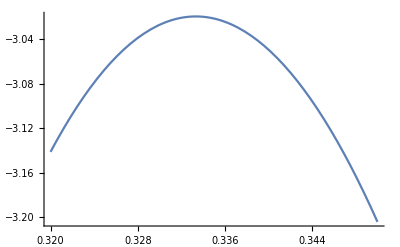

```mathematica
Plot[llBino[300,100,p],{p,.32,.35}]
```

```mathematica
Plot3D[llBino[M,100,p],{M,101,1000},{p,.01,.99}]
```

-Graphics3D-

```mathematica
FindMinimum[-(llBino[m,100,p]:=LogGamma[N+1]-LogGamma[n+1]-LogGamma[N-n+1]+(N-n)*Log[1-p]+n*Log[p]),{m,100},{p,.99}]
```

FindMinimum::nrnum: The function value -Null is not a real number at {m, p} = {100., 0.99}.

FindMinimum[-(llBino[m,100,p]:=LogGamma[N+1]-LogGamma[n+1]-LogGamma[N-n+1]+(N-n) Log[1-p]+n Log[p]),{m,100},{p,0.99}]

```mathematica
PLLBino[N_,n_]:=LogGamma[N+1]-LogGamma[N-n+1]-LogGamma[n+1]+(N-n)*Log[1-n/N]+n*Log[n/N]
```

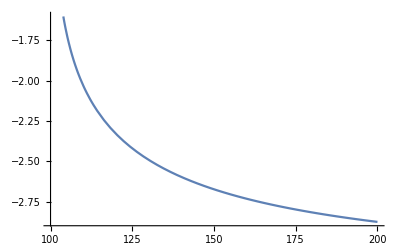

```mathematica
Plot[PLLBino[m,100],{m,100,200}]
```

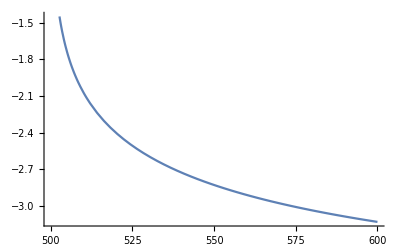

```mathematica
Plot[PLLBino[m,500],{m,500,600}]
```

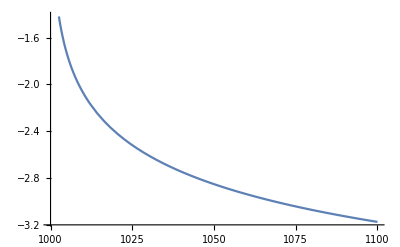

```mathematica
Plot[PLLBino[m,1000],{m,1000,1100}]
```

```mathematica
aobT[.3,6]//N
```

0.0577134

```mathematica
D[Exp[1]/(1+Exp[x]+Exp[y]+Exp[z]),x]
```

-ⅇ^(1+x)/((1+ⅇ^x+ⅇ^y+ⅇ^z)^2)

```mathematica
Sum[Exp[gamma[j]]/(1+Exp[gamma[j]]),{j,1,3}]
```

ⅇ^gamma[1]/(1+ⅇ^gamma[1])+ⅇ^gamma[2]/(1+ⅇ^gamma[2])+ⅇ^gamma[3]/(1+ⅇ^gamma[3])

```mathematica
D[Sum[Exp[gamma[j]]/(1+Exp[gamma[j]]),{j,1,3}],gamma[1]]
```

-ⅇ^(2 gamma[1])/((1+ⅇ^gamma[1])^2)+ⅇ^gamma[1]/(1+ⅇ^gamma[1])

```mathematica
Pk[k_,D_] = Sum[(1-β*Exp[γ[h]]/(1+Exp[γ[h]]))^k*(β*Exp[γ[h]]/(1+Exp[γ[h]]))^(S-k)*(Exp[ζ[h]]/Sum[Exp[ζ[l]],{l,1,D}]),{h,1,D}]
```

∑_(h=1)^D (ⅇ^ζ[h] ((ⅇ^γ[h] β)/(1+ⅇ^γ[h]))^(-k+S) (1-(ⅇ^γ[h] β)/(1+ⅇ^γ[h]))^k)/(∑_(l=1)^D ⅇ^ζ[l])

```mathematica
D[Pk[k,5],γ[1]]
```

(ⅇ^ζ[1] k ((ⅇ^γ[1] β)/(1+ⅇ^γ[1]))^(-k+S) (1-(ⅇ^γ[1] β)/(1+ⅇ^γ[1]))^(-1+k) ((ⅇ^(2 γ[1]) β)/((1+ⅇ^γ[1])^2)-(ⅇ^γ[1] β)/(1+ⅇ^γ[1])))/(ⅇ^ζ[1]+ⅇ^ζ[2]+ⅇ^ζ[3]+ⅇ^ζ[4]+ⅇ^ζ[5])+(ⅇ^ζ[1] (-k+S) ((ⅇ^γ[1] β)/(1+ⅇ^γ[1]))^(-1-k+S) (1-(ⅇ^γ[1] β)/(1+ⅇ^γ[1]))^k (-(ⅇ^(2 γ[1]) β)/((1+ⅇ^γ[1])^2)+(ⅇ^γ[1] β)/(1+ⅇ^γ[1])))/(ⅇ^ζ[1]+ⅇ^ζ[2]+ⅇ^ζ[3]+ⅇ^ζ[4]+ⅇ^ζ[5])

```mathematica
D[Pk[k,5],ζ[1]]
```

-(ⅇ^(2 ζ[1]) ((ⅇ^γ[1] β)/(1+ⅇ^γ[1]))^(-k+S) (1-(ⅇ^γ[1] β)/(1+ⅇ^γ[1]))^k)/((ⅇ^ζ[1]+ⅇ^ζ[2]+ⅇ^ζ[3]+ⅇ^ζ[4]+ⅇ^ζ[5])^2)+(ⅇ^ζ[1] ((ⅇ^γ[1] β)/(1+ⅇ^γ[1]))^(-k+S) (1-(ⅇ^γ[1] β)/(1+ⅇ^γ[1]))^k)/(ⅇ^ζ[1]+ⅇ^ζ[2]+ⅇ^ζ[3]+ⅇ^ζ[4]+ⅇ^ζ[5])-(ⅇ^(ζ[1]+ζ[2]) ((ⅇ^γ[2] β)/(1+ⅇ^γ[2]))^(-k+S) (1-(ⅇ^γ[2] β)/(1+ⅇ^γ[2]))^k)/((ⅇ^ζ[1]+ⅇ^ζ[2]+ⅇ^ζ[3]+ⅇ^ζ[4]+ⅇ^ζ[5])^2)-(ⅇ^(ζ[1]+ζ[3]) ((ⅇ^γ[3] β)/(1+ⅇ^γ[3]))^(-k+S) (1-(ⅇ^γ[3] β)/(1+ⅇ^γ[3]))^k)/((ⅇ^ζ[1]+ⅇ^ζ[2]+ⅇ^ζ[3]+ⅇ^ζ[4]+ⅇ^ζ[5])^2)-(ⅇ^(ζ[1]+ζ[4]) ((ⅇ^γ[4] β)/(1+ⅇ^γ[4]))^(-k+S) (1-(ⅇ^γ[4] β)/(1+ⅇ^γ[4]))^k)/((ⅇ^ζ[1]+ⅇ^ζ[2]+ⅇ^ζ[3]+ⅇ^ζ[4]+ⅇ^ζ[5])^2)-(ⅇ^(ζ[1]+ζ[5]) ((ⅇ^γ[5] β)/(1+ⅇ^γ[5]))^(-k+S) (1-(ⅇ^γ[5] β)/(1+ⅇ^γ[5]))^k)/((ⅇ^ζ[1]+ⅇ^ζ[2]+ⅇ^ζ[3]+ⅇ^ζ[4]+ⅇ^ζ[5])^2)

```mathematica
Pktb[1,1,aobT[6,.3],2,6]
```

2.05471×10^14-1.93739×10^12 ⅈ

```mathematica
Exp[RandomVariate[NormalDistribution[0,1],1]]
```

{0.516233}

```mathematica
Integrate[PDF[BetaDistribution[a,b],x],{x,α,1},Assumptions->{a>0,b>0,α>0,α<1}]
```

(Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b])/(Gamma[a] Gamma[b])

```mathematica
Cbeta[a_,b_,α_]:=((Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b])/(Gamma[a] Gamma[b]))^(-1)
```

```mathematica
Integrate[p^k*(1-p)^(S-k)*PDF[BetaDistribution[a,b],p]*Cbeta[a,b,α],{p,α,1},Assumptions->{a>0,b>0,α>0,α<1,S>k,k>0}]
```

-(Gamma[a] Gamma[b] (Beta[α,a+k,b-k+S] Gamma[a+b+S]-Gamma[a+k] Gamma[b-k+S]))/(Beta[a,b] (Gamma[a] Gamma[b]-Beta[α,a,b] Gamma[a+b]) Gamma[a+b+S])

```mathematica
0.7*Pktb[5,2,aobT[.1,7],{0,1,2,3,4,5,6,7},7]+0.3*Pktb[2,10,aobT[.1,7],{0,1,2,3,4,5,6,7},7]
```

{0.109153,0.109492,0.0939661,0.0986536,0.124706,0.157342,0.171996,0.134692}

```mathematica
Integrate[PDF[BetaDistribution[a,b],x],{x,c,1},Assumptions->{c>0,c<1,a>0,b>0}]
```

(Gamma[a] Gamma[b]-Beta[c,a,b] Gamma[a+b])/(Gamma[a] Gamma[b])

```mathematica
Integrate[x^k*PDF[BetaDistribution[a,b],x],{x,0,1},Assumptions->{a>0,b>0,k->Integers,k>0}]
```

(Gamma[b] Gamma[a+k])/(Beta[a,b] Gamma[a+b+k])

```mathematica
Mr[a_,b_,k_]:=(Gamma[b] Gamma[a+k])/(Beta[a,b] Gamma[a+b+k])
```

```mathematica
NSolve[{Mr[1,1,1]==c*Mr[1/2,1,1],Mr[1,1,2]==c*Mr[1/2,1,1]},c]
```

{}

```mathematica
Solve[{(a[1]+1)/(a[1]+b[1]+1)==(a[2]+1)/(a[2]+b[2]+1),(a[1]+2)/(a[1]+b[1]+2)==(a[2]+2)/(a[2]+b[2]+2)},{a[1],b[1]}]
```

{{a[1]→a[2],b[1]→b[2]}}

```mathematica
D[LogGamma[N+1]-LogGamma[N-n+1]+(N-n)*Log[1-n/N]+n*Log[n/N],N]
```

-n/N+(n (-n+N))/((1-n/N) N^2)+Log[1-n/N]+PolyGamma[0,1+N]-PolyGamma[0,1-n+N]

```mathematica
Dlg[n_,N_]:=-n/N+(n (-n+N))/((1-n/N) N^2)+Log[1-n/N]+PolyGamma[0,1+N]-PolyGamma[0,1-n+N]
```

```mathematica
Limit[Dlg[1000,N],N->1000]
```

-∞

```mathematica
Limit[Dlg[1000,N],N->Infinity]
```

0

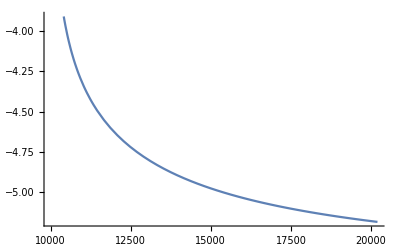

```mathematica
Plot[PLLBino[m,10000],{m,10000,20200}]
```

```mathematica
Betadensp0[a_,b_,t_,x_]:=(1/t)*(1-x)^(1/t-1)*PDF[BetaDistribution[a,b],1-(1-x)^(1/t)]
```

```mathematica
Integrate[Betadensp0[a,b,t,x],{x,0,1},Assumptions->{t->Integers,t>1,a>0,b>0}]
```

Integrate[((1-x)^(-1+1/t) (Piecewise[{{((1-(1-x)^(1/t))^(-1+a) ((1-x)^(1/t))^(-1+b))/Beta[a,b], 0<1-(1-x)^(1/t)<1}, {0, True}}]))/t,{x,0,1},Assumptions→{t→Integers,t>1,a>0,b>0}]

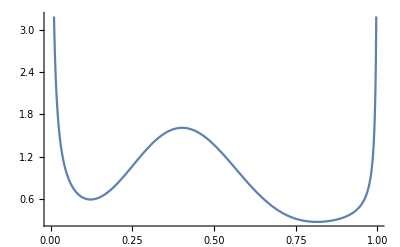

```mathematica
Plot[0.6*Betadensp0[1/5,1,6,x]+0.5*Betadensp0[5,50,6,x],{x,0,1}]
```

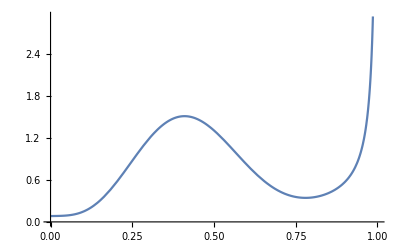

```mathematica
Plot[0.5*Betadensp0[1,1,6,x]+0.5*Betadensp0[5,50,6,x],{x,0,1}]
```

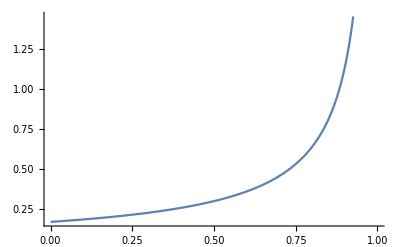

```mathematica
Plot[Betadensp0[1,1,6,x],{x,0,1}]
```

```mathematica
Atomdensp0[μ_,t_] := 1-(1-μ)^t
```

```mathematica
DiscretePlot[0.3*Atomdensp0[.1,6]+.2*Atomdensp0[.2,6]+.5*Atomdensp0[.5,6]]
```

DiscretePlot[0.3 Atomdensp0[0.1,6]+0.2 Atomdensp0[0.2,6]+0.5 Atomdensp0[0.5,6]]

```mathematica
Atomdensp0[.01,6]
```

0.0585199

```mathematica
Pkatom[p_,k_,S_] := p^k*(1-p)^(S-k)*Binomial[S,k]
```

```mathematica
.3*Pkatom[.1,{0,1,2,3,4,5,6},6]+.2*Pkatom[.2,{0,1,2,3,4,5,6},6]+.5*Pkatom[.5,{0,1,2,3,4,5,6},6]
```

{0.219674,0.231806,0.195864,0.177008,0.120624,0.0471984,0.0078256}

```mathematica
.3*Pkatom[.01,{0,1,2,3,4,5,6},6]+.2*Pkatom[.1,{0,1,2,3,4,5,6},6]+.5*Pkatom[.6,{0,1,2,3,4,5,6},6]
```

{0.39078,0.106409,0.0892353,0.141162,0.155763,0.0933228,0.0233282}

```mathematica
0.6*Pktb[1/5,1,0,{0,1,2,3,4,5,6},6]+0.4*Pktb[5,50,0,{0,1,2,3,4,5,6},6]//N
```

{0.609268,0.201868,0.0804118,0.039413,0.0272994,0.0223828,0.0193565}

```mathematica
0.5*Pktb[1,1,0,{0,1,2,3,4,5,6},6]+0.5*Pktb[5,50,0,{0,1,2,3,4,5,6},6]//N
```

{0.360956,0.229352,0.115296,0.0791537,0.0723199,0.0714915,0.0714307}

```mathematica
Pktb[1,1,0,{0,1,2,3,4,5,6},6]//N
```

{0.142857,0.142857,0.142857,0.142857,0.142857,0.142857,0.142857}

```mathematica
Betpalpha[a_,b_,α_,S_]:=1-CDF[BetaDistribution[a,b],aobT[α,S]]
```

```mathematica
.5*Betpalpha[1,1,{.005,.01,.05,.1},6]+.5*Betpalpha[5,50,{.005,.01,.05,.1},6]
```

{0.999582,0.999163,0.995694,0.990052}

```mathematica
.6*Betpalpha[1/5,1,{.005,.01,.05,.1},6]+.5*Betpalpha[5,50,{.005,.01,.05,.1},6]
```

{0.954623,0.932935,0.868657,0.831888}

```mathematica
Betpalpha[1,1,{.005,.01,.05,.1},6]
```

{0.999165,0.998326,0.991488,0.982593}

```mathematica
aobT[{.005,.01,.05,.1},6]
```

{0.000835075,0.00167365,0.00851244,0.0174068}

```mathematica
Atompalpha[p_,α_,S_]:=(1-(1-p)^S)*(p>1-(1-α)^(1/S))
```

```mathematica
(1>.5)*1
```

True

```mathematica
Integrate[(1+Exp[x])/Exp[x],{x,a,b}]//FullSimplify
```

-a+b+Cosh[a]-Cosh[b]-Sinh[a]+Sinh[b]

```mathematica
fln[x_,μ_,v_]:=1/(Sqrt[v*2*Pi])*Exp[-(Log[x/(1-x)]-μ)^2/(2*v)]*(1/(x*(1-x)))
```

```mathematica
D[Log[fln[x,μ,ν]],x]//FullSimplify
```

(-μ+ν-2 x ν+Log[1/(1-x)]+Log[x])/((-1+x) x ν)

```mathematica
Solve[(-μ+ν-2 x ν+Log[1/(1-x)]+Log[x])/((-1+x) x ν)==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(-μ+ν-2 x ν+Log[1/(1-x)]+Log[x])/((-1+x) x ν)==0,x]

```mathematica
PolyGamma[0,.5]
```

-1.96351

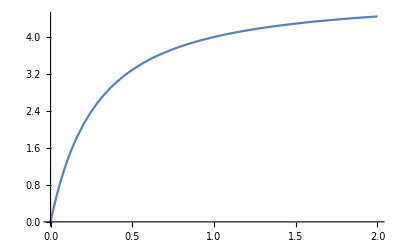

```mathematica
Plot[PolyGamma[1,1/2]-PolyGamma[1,1/2+b],{b,0,2}]
```

```mathematica
Solve[M+B*(Z-M)==(A^(-1)+n/s)^(-1)*(A^(-1)*M+n/s*Z),B]
```

{{B→(A n)/(A n+s)}}

```mathematica
Solve[(A^(-1)+n/s)^(-1)==B*s,B]
```

{{B→A/(A n+s)}}

```mathematica
PkF[k_,S_,m_]:=Sum[S!/(r!*((r-k)!)*((S-r)!))*(-1)^(r-k)*m[[r]],{r,k,S}]
```

```mathematica
Expand[PkF[3,7,Table[M[i],{i,0,7}]]]
```

PkF[3,7,{M[0],M[1],M[2],M[3],M[4],M[5],M[6],M[7]}]

```mathematica
M[0] = 0
```

0

```mathematica
m=Table[M[i],{i,0,6}]
```

{0,M[1],M[2],M[3],M[4],M[5],M[6]}

```mathematica
PkF[0,6,m]
```

List+(15 M[1])/2-(10 M[2])/3+(5 M[3])/8-M[4]/20+M[5]/720

```mathematica
PkF[2,6,m]
```

15 M[2]-20 M[3]+(15 M[4])/2-M[5]+M[6]/24

```mathematica
Moment[BetaDistribution[a,b],1]
```

a/(a+b)

```mathematica
Moment[BetaDistribution[a,b],2]
```

(a (1+a))/((a+b) (1+a+b))

```mathematica
Moment[BetaDistribution[a,b],k]
```

Pochhammer[a,k]/Pochhammer[a+b,k]

```mathematica
Solve[(a+b+2)/(a+2)==z[2]&&(a+b+1)*(a+b+2)/((a+1)*(a+2))==z[1],{a,b}]
```

{{a→(-z[1]-z[2]+2 z[2]^2)/(z[1]-z[2]^2),b→((z[1]-z[2]) (-1+z[2]))/(z[1]-z[2]^2)}}

```mathematica
Solve[(a+b+2)/(a+2)==x[2]/3+1&&(a+b+1)*(a+b+2)/((a+1)*(a+2))==(2/6)*x[1]+(2/3)*x[2]+2,{a,b}]
```

{{a→(-9-3 x[1]+3 x[2]+2 x[2]^2)/(9+3 x[1]-x[2]^2),b→-(x[2] (3+x[1]+x[2]))/(-9-3 x[1]+x[2]^2)}}

```mathematica
Solve[a[2]/(a[2]+b[2]) == γ*a[1]/(a[1]+b[1])&&a[2]*(a[2]+1)/((a[2]+b[2])*(a[2]+b[2]+1))==γ*a[1]*(a[1]+1)/((a[1]+b[1])*(a[1]+b[1]+1)),{a[2],b[2]}]//FullSimplify
```

{{a[2]→-(γ a[1] b[1])/(-b[1]+(-1+γ) a[1] (1+a[1]+b[1])),b[2]→(((-1+γ) a[1]-b[1]) b[1])/(-b[1]+(-1+γ) a[1] (1+a[1]+b[1]))}}

```mathematica
Solve[a[2]/(a[2]+b[2]) == γ*a[1]/(a[1]+b[1])&&a[2]*(a[2]+1)/((a[2]+b[2])*(a[2]+b[2]+1))==γ*a[1]*(a[1]+1)/((a[1]+b[1])*(a[1]+b[1]+1))&&Product[a[2]+j,{j,0,2}]/Product[a[2]+b[2]+j,{j,0,2}]==γ*Product[a[1]+j,{j,0,2}]/Product[a[1]+b[1]+j,{j,0,2}],{a[2],b[2],γ}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a[2]→0,γ→0},{a[2]→a[1],b[2]→b[1],γ→1}}

```mathematica
Solve[a[2]/(a[2]+b[2]) == a[1]/(a[1]+b[1])&&a[2]*(a[2]+1)/((a[2]+b[2])*(a[2]+b[2]+1))==a[1]*(a[1]+1)/((a[1]+b[1])*(a[1]+b[1]+1))&&Product[a[2]+j,{j,0,2}]/Product[a[2]+b[2]+j,{j,0,2}]==Product[a[2]+j,{j,0,2}]/Product[a[2]+b[2]+j,{j,0,2}],{a[2],b[2]}]//FullSimplify
```

{{a[2]→a[1],b[2]→b[1]}}

```mathematica
Solve[Sum[4!/(1!*(r-1)!*(4-r)!)*(-1)^(r-1)*z[r],{r,1,3}]+Binomial[4,1]*(-1)^(4-1)==x[1]&&Sum[4!/(2!*(r-2)!*(4-r)!)*(-1)^(r-2)*z[r],{r,2,3}]+Binomial[4,2]*(-1)^(4-2)==x[2] && Sum[4!/(3!*(r-3)!*(4-r)!)*(-1)^(r-3)*z[r],{r,3,3}]+Binomial[4,3]*(-1)^(4-3)==x[3],{z[1],z[2],z[3]}]//FullSimplify
```

{{z[1]→1/4 (4+x[1]+2 x[2]+3 x[3]),z[2]→1/6 (6+x[2]+3 x[3]),z[3]→1/4 (4+x[3])}}

```mathematica
RSolve[{z[1]==T^(-1)*x[1]+1,z[k]==x[k]-(-1)^k*Binomial[T,T-k]-Sum[T!/((T-k-1)!*(r-(T-k-1))!*(T-r)!)*(-1)^(r-(T-k-1))*z[T-r],{r,T-k+1,T-1}]},z[T-1],T]
```

RSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in z[-1 + T] should literally match the independent variables.

RSolve[{z[1]==1+x[1]/T,(-1)^(1+k) Binomial[T,-k+T]-∑_(r=1-k+T)^(-1+T) ((-1)^(k+r-T) T! z[r])/((k+r-T)! (-k+T)! (-r+T)!)+x[k]==(-1)^(1+k) Binomial[T,-k+T]-∑_(r=1-k+T)^(-1+T) ((-1)^(1+k+r-T) T! z[-r+T])/((1+k+r-T)! (-1-k+T)! (-r+T)!)+x[k]},z[-1+T],T]

```mathematica
m[k_]=ν*Pochhammer[a[1],k]/Pochhammer[a[1]+b[1],k]+(1-ν)*Pochhammer[a[2],k]/Pochhammer[a[2]+b[2],k]
```

(ν Pochhammer[a[1],k])/Pochhammer[a[1]+b[1],k]+((1-ν) Pochhammer[a[2],k])/Pochhammer[a[2]+b[2],k]

```mathematica
m[1]
```

(ν a[1])/(a[1]+b[1])+((1-ν) a[2])/(a[2]+b[2])

```mathematica
Solve[m[1]==p[1]&&m[2]==p[2]&&m[3]==p[3]&&m[4]==p[4]&&m[5]==p[5],{a[1],a[2],b[1],b[2],ν}]
```

$Aborted

```mathematica
ma[k_]:=  ν[1]*q[1]^k+ν[2]*q[2]^k+(1-ν[1]-ν[2])*q[3]^k
```

```mathematica
Solve[ma[1]==p[1]&&ma[2]==p[2]&&ma[3]==p[3]&&ma[4]==p[4]&&ma[5]==p[5],{q[1],q[2],q[3],ν[1],ν[2]}]
```

$Aborted

```mathematica
Integrate[p^k*(1-p)^(3-k)*PDF[BetaDistribution[a,b],p],{p,0,1},Assumptions->{a>0,b>0,k>=0,k≤3, k->Integers}]//FullSimplify
```

(Gamma[3+b-k] Gamma[a+k])/(Beta[a,b] Gamma[3+a+b])

```mathematica
(Gamma[3+b-k] Gamma[a+k])/(Beta[a,b] Gamma[3+a+b])/(1-(Gamma[3+b] Gamma[a])/(Beta[a,b] Gamma[a+b]))//FullSimplify
```

(Gamma[a+b] Gamma[3+b-k] Gamma[a+k])/(Gamma[a] (Gamma[b]-Gamma[3+b]) Gamma[3+a+b])

```mathematica
pkc[a_,b_,k_] := (Gamma[a+b] Gamma[3+b-k] Gamma[a+k])/(Gamma[a] (Gamma[b]-Gamma[3+b]) Gamma[3+a+b])
```

```mathematica
pkc[1,1,1]//N
```

-0.0166667

```mathematica
Integrate[(1-p)^3*PDF[BetaDistribution[a,b],p],{p,0,1},Assumptions->{a>0,b>0}]//FullSimplify
```

(Gamma[a] Gamma[3+b])/(Beta[a,b] Gamma[3+a+b])

```mathematica
Integrate[p^k*(1-p)^(3-k),{p,0,1},Assumptions->{k≤3,k≥0,k->Integers}]
```

1/24 Gamma[4-k] Gamma[1+k]

```mathematica
pkc[k_]:=1/24 Gamma[4-k] Gamma[1+k]
```

```mathematica
pkc[1]/(1-pkc[0])//N
```

0.111111

```mathematica
pkc[2]/(1-pkc[0])
```

1/9

```mathematica
pkc[2]//N
```

0.0833333

```mathematica
pkc[1]//N
```

0.0833333

```mathematica
pkc[3]/(1-pkc[0])
```

1/3

```mathematica
pkc[0]
```

1/4

```mathematica
Solve[ν*p[1]*(1-p[1])^2+(1-ν)*p[2]*(1-p[2])^2==.99*8/57 *(1-(ν*(1-p[1])^3 + (1-ν)*(1-p[2])^3))&& ν*p[1]^2*(1-p[1])+(1-ν)*p[2]^2*(1-p[2])==.99*2/19*(1-(ν*(1-p[1])^3 + (1-ν)*(1-p[2])^3)) && ν*p[1]^3+(1-ν)*p[2]^3==.99*5/19*(1-(ν*(1-p[1])^3 + (1-ν)*(1-p[2])^3)),{p[1],p[2],ν}]
```

{{p[1]→0.,ν→1.},{p[2]→0.,ν→0.},{p[1]→0.,p[2]→0.}}

```mathematica
Gamma[4]*Gamma[1]/24
```

1/4

```mathematica
Gamma[3]*Gamma[2]/24
```

1/12

```mathematica
pkc[a_,b_,k_]:=(Gamma[3+b-k] Gamma[a+k])/(Beta[a,b] Gamma[3+a+b])
```

```mathematica
pkc[1/2,1,1]/(1-pkc[1/2,1,0])
```

8/57

```mathematica
pkc[1/2,1,2]/(1-pkc[1/2,1,0])
```

2/19

```mathematica
pkc[1/2,1,3]/(1-pkc[1/2,1,0])
```

5/19

```mathematica
nuBeta[k_,a_,b_,T_]:=Binomial[T,k]* Integrate[q^k*(1-q)^(T-k)*PDF[BetaDistribution[a,b],q],{q,0,1}]
```

```mathematica
nuBeta[{0,1,2,3,4,5,6},1/2,1/2,6]//N
```

{0.225586,0.123047,0.102539,0.0976563,0.102539,0.123047,0.225586}

```mathematica
nuBeta[{0,1,2,3,4,5,6},1,10,6]//N
```

{0.625,0.25,0.0892857,0.0274725,0.00686813,0.00124875,0.000124875}

```mathematica
nuBeta[{0,1,2,3,4,5,6},1,1,6]//N
```

{0.142857,0.142857,0.142857,0.142857,0.142857,0.142857,0.142857}

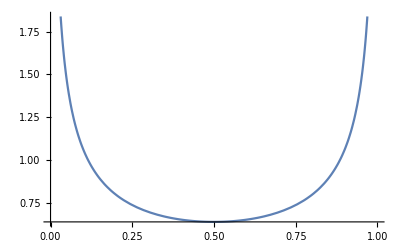

```mathematica
Plot[PDF[BetaDistribution[1/2,1/2],x],{x,0,1}]
```

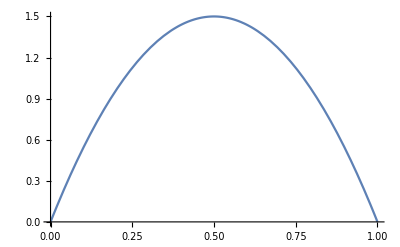

```mathematica
Plot[PDF[BetaDistribution[2,2],x],{x,0,1}]
```

```mathematica
pobBeta[α_,a_,b_,T_]:=1-BetaRegularized[1-(1-α)^(1/T),a,b]
```

```mathematica
pobBeta[{.005,.01,.05,.1},1/2,1/2,6]//N
```

{0.981601,0.973948,0.94118,0.915762}

```mathematica
pobBeta[{.005,.01,.05,.1},2,2,6]//N
```

{0.999998,0.999992,0.999784,0.999102}

```mathematica
pobBeta[{.005,.01,.05,.1},1,1,6]//N
```

{0.999165,0.998326,0.991488,0.982593}

```mathematica
Plot[pobBeta[α,1/2,1/2,6],{α,0,1}]
```

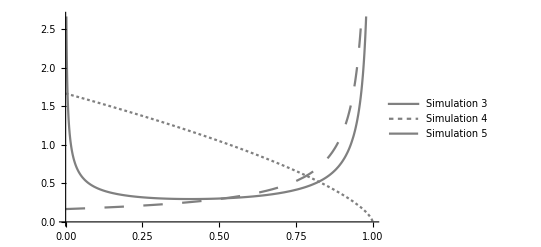

```mathematica
Plot[{Betadensp0[1/2,1/2,6,x],Betadensp0[1,10,6,x],Betadensp0[1,1,6,x]},{x,0,1},BaseStyle->{FontWeight->"Bold",FontSize->14},PlotStyle->{Gray,{Gray,Dashing[Tiny]},{Gray,Dashing[Large]}},PlotLegends->{"Simulation 3","Simulation 4","Simulation 5"}]
```

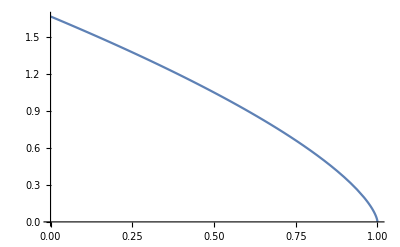

```mathematica
Plot[Betadensp0[1,10,6,x],{x,0,1}]
```

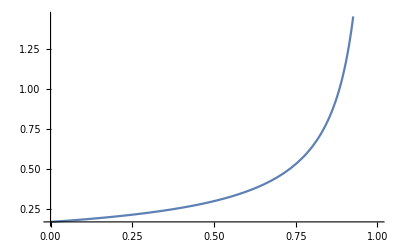

```mathematica
Plot[Betadensp0[1,1,6,x],{x,0,1}]
```

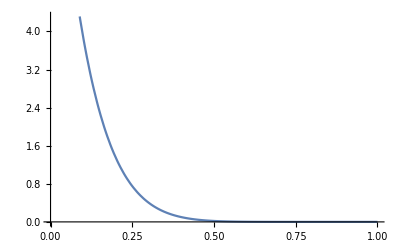

```mathematica
Plot[PDF[BetaDistribution[1,10],x],{x,0,1}]
```

```mathematica
Integrate[q^k*(1-q)^(T-k)*PDF[BetaDistribution[a,b],q],{q,0,1}]
```

Piecewise[{{(Gamma[a+k] Gamma[b-k+T])/(Beta[a,b] Gamma[a+b+T]), Re[b-k+T]>0&&Re[a+k]>0}, {Integrate[(1-q)^(-k+T) q^k (Piecewise[{{((1-q)^(-1+b) q^(-1+a))/Beta[a,b], 0<q<1}, {0, True}}]),{q,0,1},Assumptions→Re[a+k]≤0||Re[b-k+T]≤0], True}}]